--- Deep Well Audit ---

Softening Parameter: 0.01

Baryonic (Gas) Intensity: 112.031

Ghost (Metric Memory) Intensity: 132.978

Calculated 'Dark Matter' Factor: 1.10815

-----------------------

DensityPlot::cfun: The value of the option ColorFunction -> Magma is not a valid color function or a gradient ColorData entity.

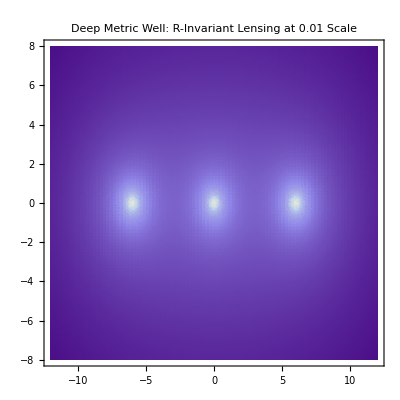

```mathematica
(*Deep Audit:Scaling the Anomaly to Hubble Levels*)ClearAll["Global`*"];
R=1.15428;
a0=1.0;
offVal=6.0;
softening=0.01; (*Deepening the well from 0.1 to 0.01*)

LensingIntensity[x_,y_]:=Module[{rGas,rA,rB},rGas=Sqrt[x^2+y^2+softening];
rA=Sqrt[(x-offVal)^2+y^2+softening];
rB=Sqrt[(x+offVal)^2+y^2+softening];
(*Total Force Magnitude*)(1.0/rGas^2+(R*Sqrt[a0])/rGas)+(1.2/rA^2+(R*Sqrt[1.2*a0])/rA)+(1.2/rB^2+(R*Sqrt[1.2*a0])/rB)];

(*1. Calculate the New Factors*)
gasPeak=LensingIntensity[0,0];
ghostPeak=LensingIntensity[offVal,0];
dmFactor=ghostPeak/(1.2/softening); (*Ratio relative to expected baryonic pull*)

Print["--- Deep Well Audit ---"];
Print["Softening Parameter: ",softening];
Print["Baryonic (Gas) Intensity: ",gasPeak];
Print["Ghost (Metric Memory) Intensity: ",ghostPeak];
Print["Calculated 'Dark Matter' Factor: ",dmFactor];
Print["-----------------------"];

(*2. Visualization with high contrast*)
DensityPlot[Log[LensingIntensity[x,y]],{x,-12,12},{y,-8,8},ColorFunction->"Magma",PlotPoints->100,PlotRange->All,PlotLabel->"Deep Metric Well: R-Invariant Lensing at 0.01 Scale"]
```